# P295a PS 6

## Gabriel Patenotte

## 1.

```mathematica
n=8;
s=IdentityMatrix[n];
s={#}ᵀ&/@s;
conj=Complex[a_,b_]->Complex[a,-b];
hc[state_]:=Transpose[state/.conj]
bra[j_]:=hc[s[[j]]];
ket[j_]:=s[[j]];
H=-t Sum[Exp[ⅈ ϕ]ket[Mod[j+1,n,1]].bra[Mod[j,n,1]]+Exp[-ⅈ ϕ]ket[Mod[j,n,1]].bra[Mod[j+1,n,1]],{j,1,n}];
MatrixForm[H]
```

(0 | -ⅇ^(-ⅈ ϕ) t | 0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ ϕ) t
-ⅇ^(ⅈ ϕ) t | 0 | -ⅇ^(-ⅈ ϕ) t | 0 | 0 | 0 | 0 | 0
0 | -ⅇ^(ⅈ ϕ) t | 0 | -ⅇ^(-ⅈ ϕ) t | 0 | 0 | 0 | 0
0 | 0 | -ⅇ^(ⅈ ϕ) t | 0 | -ⅇ^(-ⅈ ϕ) t | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^(ⅈ ϕ) t | 0 | -ⅇ^(-ⅈ ϕ) t | 0 | 0
0 | 0 | 0 | 0 | -ⅇ^(ⅈ ϕ) t | 0 | -ⅇ^(-ⅈ ϕ) t | 0
0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ ϕ) t | 0 | -ⅇ^(-ⅈ ϕ) t
-ⅇ^(-ⅈ ϕ) t | 0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ ϕ) t | 0)

```mathematica
eval[m_,ϕ_]:=-2t Cos[(2π m)/n-ϕ];
evec[m_]:=1/(√n)Sum[Exp[ⅈ (2π m)/n k]bra[k],{k,1,n}];
```

```mathematica
list=eval[#,ϕ]&/@Range[1,n]/.t->1;order=OrderingBy[list/.ϕ->0//N,Greater];
```

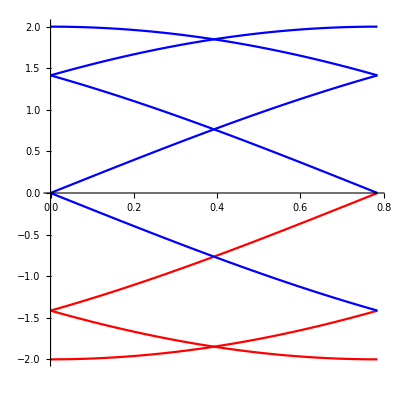

```mathematica
Plot[Evaluate@list[[order]],{ϕ,0,2 π/n},AspectRatio->1,PlotStyle->{Red,Red,Red,Blue,Blue,Blue,Blue,Blue}]
```

The bottom red lines cancel each other. However, the top red line depicts an electron moving between the left and right moving Fermi points.

## 2.

## 2a

```mathematica
p=.;q=.;ty=.;tx=.;t2=.;
```

```mathematica
hof[kx_,ky_]:=Table[If[i==j,-2 ty Cos[ky+(2 π (i-1) p)/q],If[Mod[i-j,q]==1,-tx ⅇ^(ⅈ kx),If[Mod[i-j,q]==q-1,-tx ⅇ^(-ⅈ kx),If[Mod[i-j,q]==2,-t2 ⅇ^(2 ⅈ kx),If[Mod[i-j,q]==q-2,-t2 ⅇ^(-2 ⅈ kx),0]]]]],{i,1,q},{j,1,q}]
```

```mathematica
p=1;q=5;
```

```mathematica
MatrixForm@hof[kx,ky]/.t2->0
```

(-2 ty Cos[ky] | -ⅇ^(-ⅈ kx) tx | 0 | 0 | -ⅇ^(ⅈ kx) tx
-ⅇ^(ⅈ kx) tx | 2 ty Sin[ky-π/10] | -ⅇ^(-ⅈ kx) tx | 0 | 0
0 | -ⅇ^(ⅈ kx) tx | 2 ty Cos[ky-π/5] | -ⅇ^(-ⅈ kx) tx | 0
0 | 0 | -ⅇ^(ⅈ kx) tx | 2 ty Cos[ky+π/5] | -ⅇ^(-ⅈ kx) tx
-ⅇ^(-ⅈ kx) tx | 0 | 0 | -ⅇ^(ⅈ kx) tx | -2 ty Sin[ky+π/10])

## 2b

```mathematica
tx=1.;ty=1.;t2=.0;
```

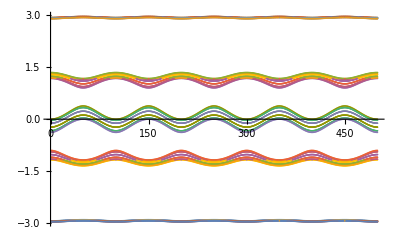

```mathematica
ListPlot[Transpose[Table[Flatten[Table[Eigenvalues[hof[2π j/50,(2π l)/500]],{j,1,10}]],{l,1,500}]]]
```

## 2c

```mathematica
npts=50;dxhof[kx_,ky_] = D[hof[kx,ky],kx];dyhof[kx_,ky_] = D[hof[kx,ky],ky];
```

```mathematica
chern[n_] := Module[{m,sum,kx,ky,ix,iy,vals,vecs,dhx,dhy},
sum=0;
Do[
kx=2 Pi ix/(npts q); 
ky=2 Pi iy/(npts q);
{vals,vecs}=Transpose[Sort[Transpose[Eigensystem[hof[kx,ky]]]]];
dhx=dxhof[kx,ky];
dhy=dyhof[kx,ky];
Do[
If[m≠n,
sum += (Conjugate[vecs[[n]]].dhx.vecs[[m]]Conjugate[vecs[[m]]].dhy.vecs[[n]]- Conjugate[vecs[[n]]].dhy.vecs[[m]]Conjugate[vecs[[m]]].dhx.vecs[[n]])/((vals[[n]]-vals[[m]])^2)
, ]
,{m,1,q}]
,{ix,1,npts},{iy,1,q npts}];
2 Pi I sum/ ((q npts)^2)]
```

```mathematica
Do[Print["band = ", n," Chern number = ",Chop[chern[n]]],{n,1,q}]
```

band = 1 Chern number = -1.

band = 2 Chern number = -1.

band = 3 Chern number = 4.

band = 4 Chern number = -1.

band = 5 Chern number = -1.

The Hall conductivity σ_xy is given by e^2/h∑_(occ. bands) c_n

```mathematica
cns={-1,-1,4,-1,-1};
```

The conductivity between each band is given by:

```mathematica
e^2/h Accumulate[cns]
```

{-e^2/h,-(2 e^2)/h,(2 e^2)/h,e^2/h,0}

## 2d

```mathematica
L=.;t2=0;
```

```mathematica
Hstrip[ky_] :=  Table[If[i==j,-2 ty Cos[ky + 2 Pi (i-1) p/q],If[Abs[i-j]==1,-tx,If[Abs[i-j]==2,-t2,0]]],{i,1,q L},{j,1,q L}]
```

```mathematica
L=50;
```

## 2e

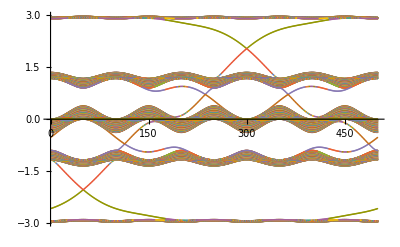

```mathematica
ListPlot[Transpose[Table[Eigenvalues[Hstrip[(2π l)/500]], {l,1,500}]]]
```

The number of edge states (or intersections in the band gaps) matches the Hall conductivities: 1, 2, 2, then 1.

## 2f

The wavefunction is clearly localized on the edges.

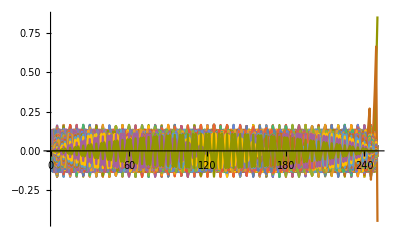
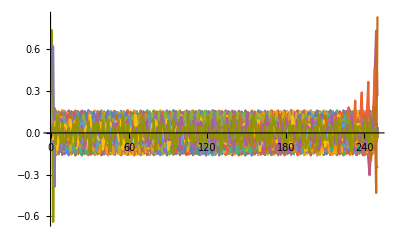
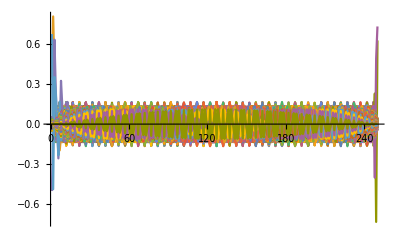

```mathematica
ListPlot[Eigenvectors[Hstrip[(2π #)/500]],PlotRange->All,Joined->True]&/@{100,220,400}
```

## 2g

### Repeat b

```mathematica
tx=1.;ty=1.;t2=.5;
```

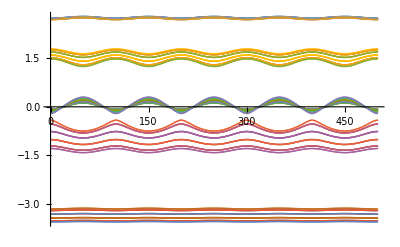

```mathematica
ListPlot[Transpose[Table[Flatten[Table[Eigenvalues[hof[2π j/50,(2π l)/500]],{j,1,10}]],{l,1,500}]]]
```

### Repeat c

```mathematica
npts=50;dxhof[kx_,ky_] = D[hof[kx,ky],kx];dyhof[kx_,ky_] = D[hof[kx,ky],ky];
```

```mathematica
chern[n_] := Module[{m,sum,kx,ky,ix,iy,vals,vecs,dhx,dhy},
sum=0;
Do[
kx=2 Pi ix/(npts q); 
ky=2 Pi iy/(npts q);
{vals,vecs}=Transpose[Sort[Transpose[Eigensystem[hof[kx,ky]]]]];
dhx=dxhof[kx,ky];
dhy=dyhof[kx,ky];
Do[
If[m≠n,
sum += (Conjugate[vecs[[n]]].dhx.vecs[[m]]Conjugate[vecs[[m]]].dhy.vecs[[n]]- Conjugate[vecs[[n]]].dhy.vecs[[m]]Conjugate[vecs[[m]]].dhx.vecs[[n]])/((vals[[n]]-vals[[m]])^2)
, ]
,{m,1,q}]
,{ix,1,npts},{iy,1,q npts}];
2 Pi I sum/ ((q npts)^2)]
```

```mathematica
Do[Print["band = ", n," Chern number = ",Chop[chern[n]]],{n,1,q}]
```

band = 1 Chern number = -1.

band = 2 Chern number = 4.

band = 3 Chern number = -1.

band = 4 Chern number = -1.

band = 5 Chern number = -1.

The Hall conductivity σ_xy is given by e^2/h∑_(occ. bands) c_n

```mathematica
cns={-1,4,-1,-1,-1};
```

The conductivity between each band is given by:

```mathematica
e^2/h Accumulate[cns]
```

{-e^2/h,(3 e^2)/h,(2 e^2)/h,e^2/h,0}

The Chern numbers changed now that t2 is nonzero.

### Repeat d

```mathematica
L=.;t2=0.5;
```

```mathematica
Hstrip[ky_] :=  Table[If[i==j,-2 ty Cos[ky + 2 Pi (i-1) p/q],If[Abs[i-j]==1,-tx,If[Abs[i-j]==2,-t2,0]]],{i,1,q L},{j,1,q L}]
```

```mathematica
L=50;
```

### Repeat e

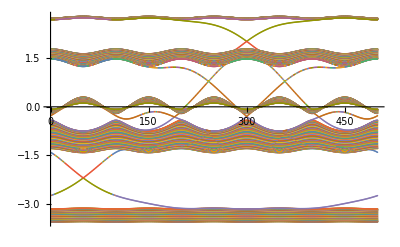

```mathematica
ListPlot[Transpose[Table[Eigenvalues[Hstrip[(2π l)/500]], {l,1,500}]]]
```

### Repeat f

The wavefunction is clearly localized on the edges.

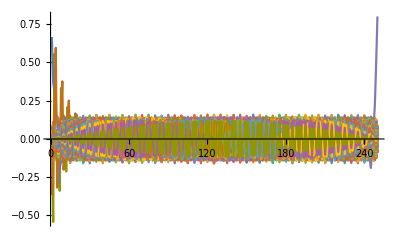
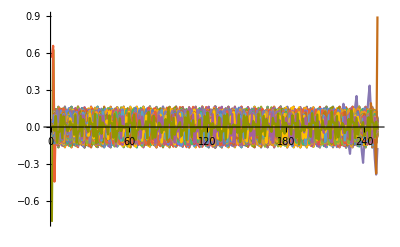
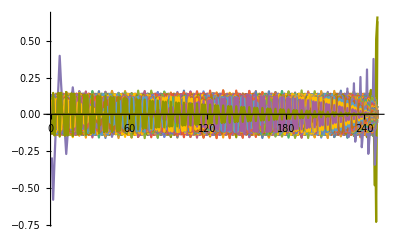

```mathematica
ListPlot[Eigenvectors[Hstrip[(2π #)/500]],PlotRange->All,Joined->True]&/@{100,220,400}
```

## 2h